For t = 50. ,  LCE = 0.874883

For t = 100. ,  LCE = 0.874439

For t = 150. ,  LCE = 0.921844

For t = 200. ,  LCE = 0.96004

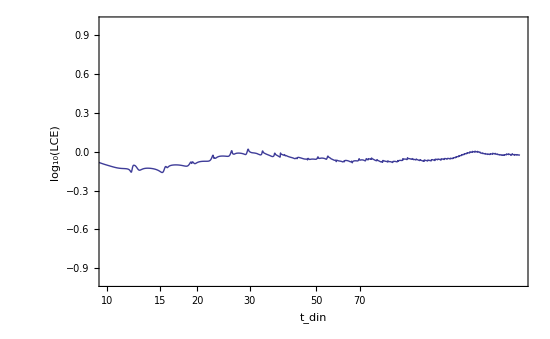

```mathematica
(*
   * Author: Panichi Federico
* Unit Name:Lyapunov
   * Unit Type: program.nb
   * Project: Master Thesis
   * Package: none
   * Language: Mathematica 9.0
   * Description: Calculate the Lyapunov Characteristic Exponent of restricted three body problem with the SHADOW PARTICLE METHOD
   * Invocation: none
*)

μ=0.000954;
SuperStar[μ]=1-μ;
Subscript[r1, 1]=√((Subscript[y1, 1][t]+μ)^2+(Subscript[y1, 2][t])^2);
Subscript[r1, 2]=√((Subscript[y1, 1][t]-SuperStar[μ])^2+(Subscript[y1, 2][t])^2);
deq1=Subscript[y1, 3][t];
deq2=Subscript[y1, 4][t];
deq3=2 Subscript[y1, 4][t]+Subscript[y1, 1][t]-(SuperStar[μ] (Subscript[y1, 1][t]+μ))/Subscript[r2, 1]^3-(μ (Subscript[y1, 1][t]-SuperStar[μ]))/Subscript[r1, 2]^3;
deq4=-2 Subscript[y1, 3][t]+Subscript[y1, 2][t]-(SuperStar[μ] Subscript[y1, 2][t])/Subscript[r1, 1]^3-(μ Subscript[y1, 2][t])/Subscript[r1, 2]^3;
Subscript[r2, 1]=√((Subscript[y2, 1][t]+μ)^2+(Subscript[y2, 2][t])^2);
Subscript[r2, 2]=√((Subscript[y2, 1][t]-SuperStar[μ])^2+(Subscript[y2, 2][t])^2);
deq5=Subscript[y2, 3][t];
deq6=Subscript[y2, 4][t];
deq7=2 Subscript[y2, 4][t]+Subscript[y2, 1][t]-(SuperStar[μ] (Subscript[y2, 1][t]+μ))/Subscript[r2, 1]^3-(μ (Subscript[y2, 1][t]-SuperStar[μ]))/Subscript[r2, 2]^3;
deq8=-2 Subscript[y2, 3][t]+Subscript[y2, 2][t]-(SuperStar[μ] Subscript[y2, 2][t])/Subscript[r2, 1]^3-(μ Subscript[y2, 2][t])/Subscript[r2, 2]^3;
a=R Cos[p]/.R->0.5 √(3+(1-3 mu)^2)/.mu->0.000954/.p->3 °;
b=R Sin[p]/.R->0.5 √(3+(1-3 mu)^2)/.mu->0.000954/.p->3 °;
c=0.3;
d=-0.3;
dx0=0.001;
e=R Cos[p]/.R->0.5 √(3+(1-3 mu)^2)/.mu->0.000954/.p->4°;
f=R Sin[p]/.R->0.5 √(3+(1-3 mu)^2)/.mu->0.000954/.p->4°;
g=0.3;
h= -0.3;
tin=0.;
tfin=240.;
tstep=0.05;
acc=13;
lcedata={};
sum=0;
d0=√((a-e)^2+(b-f)^2+(c-g)^2+(d-h)^2);
For[i=1,i<tfin/tstep,i++,sdeq={Subscript[y1, 1]'[t]==deq1,Subscript[y1, 2]'[t]==deq2,Subscript[y1, 3]'[t]==deq3,Subscript[y1, 4]'[t]==deq4,Subscript[y2, 1]'[t]==deq5,Subscript[y2, 2]'[t]==deq6,Subscript[y2, 3]'[t]==deq7,Subscript[y2, 4]'[t]==deq8,Subscript[y1, 1][0]==a,Subscript[y1, 2][0]==b,Subscript[y1, 3][0]==c,Subscript[y1, 4][0]==d,Subscript[y2, 1][0]==e,Subscript[y2, 2][0]==f,Subscript[y2, 3][0]==g,Subscript[y2, 4][0]==h};

sol=NDSolve[sdeq,{Subscript[y1, 1][t],Subscript[y1, 2][t],Subscript[y1, 3][t],Subscript[y1, 4][t],Subscript[y2, 1][t],Subscript[y2, 2][t],Subscript[y2, 3][t],Subscript[y2, 4][t]},{t,0,tstep},MaxSteps->∞,Method->"Adams",PrecisionGoal->acc,AccuracyGoal->acc];

xx1[t_]=Subscript[y1, 1][t]/.sol⟦1⟧;yy1[t_]=Subscript[y1, 2][t]/.sol⟦1⟧;zz1[t_]=Subscript[y1, 3][t]/.sol⟦1⟧;kk1[t_]=Subscript[y1, 4][t]/.sol⟦1⟧;xx2[t_]=Subscript[y2, 1][t]/.sol⟦1⟧;yy2[t_]=Subscript[y2, 2][t]/.sol⟦1⟧;zz2[t_]=Subscript[y2, 3][t]/.sol⟦1⟧;kk2[t_]=Subscript[y2, 4][t]/.sol⟦1⟧;d1=√((xx1[tstep]-xx2[tstep])^2+(yy1[tstep]-yy2[tstep])^2+(zz1[tstep]-zz2[tstep])^2+(kk1[tstep]-kk2[tstep])^2);
sum+=Log[d1/d0];

dlce=sum/(tstep i);
AppendTo[lcedata,{tstep i,Log10[dlce]}];
w1=((xx1[tstep]-xx2[tstep]) d0)/d1;w2=((yy1[tstep]-yy2[tstep]) d0)/d1;w3=((zz1[tstep]-zz2[tstep]) d0)/d1;w4=((kk1[tstep]-kk2[tstep]) d0)/d1;a=xx1[tstep];b=yy1[tstep];c=zz1[tstep];d=kk1[tstep];e=a+w1;f=b+w2;g=c+w3;h=d+w4;i=i++;If[Mod[tstep i,50]==0,Print[" For t = ",tstep i," , "," LCE = ",dlce]]]
S2=ListLogLinearPlot[{lcedata},Frame->True,Axes->True,PlotRange->{{10,240},{-1,1}},Joined->True,FrameLabel->{"\!\(\*SubscriptBox[\(t\), \(din\)]\)","\!\(\*SubscriptBox[\(log\), \(10\)]\)(LCE)"},FrameStyle->Directive["Helvetica",17],ImageSize->550]
```